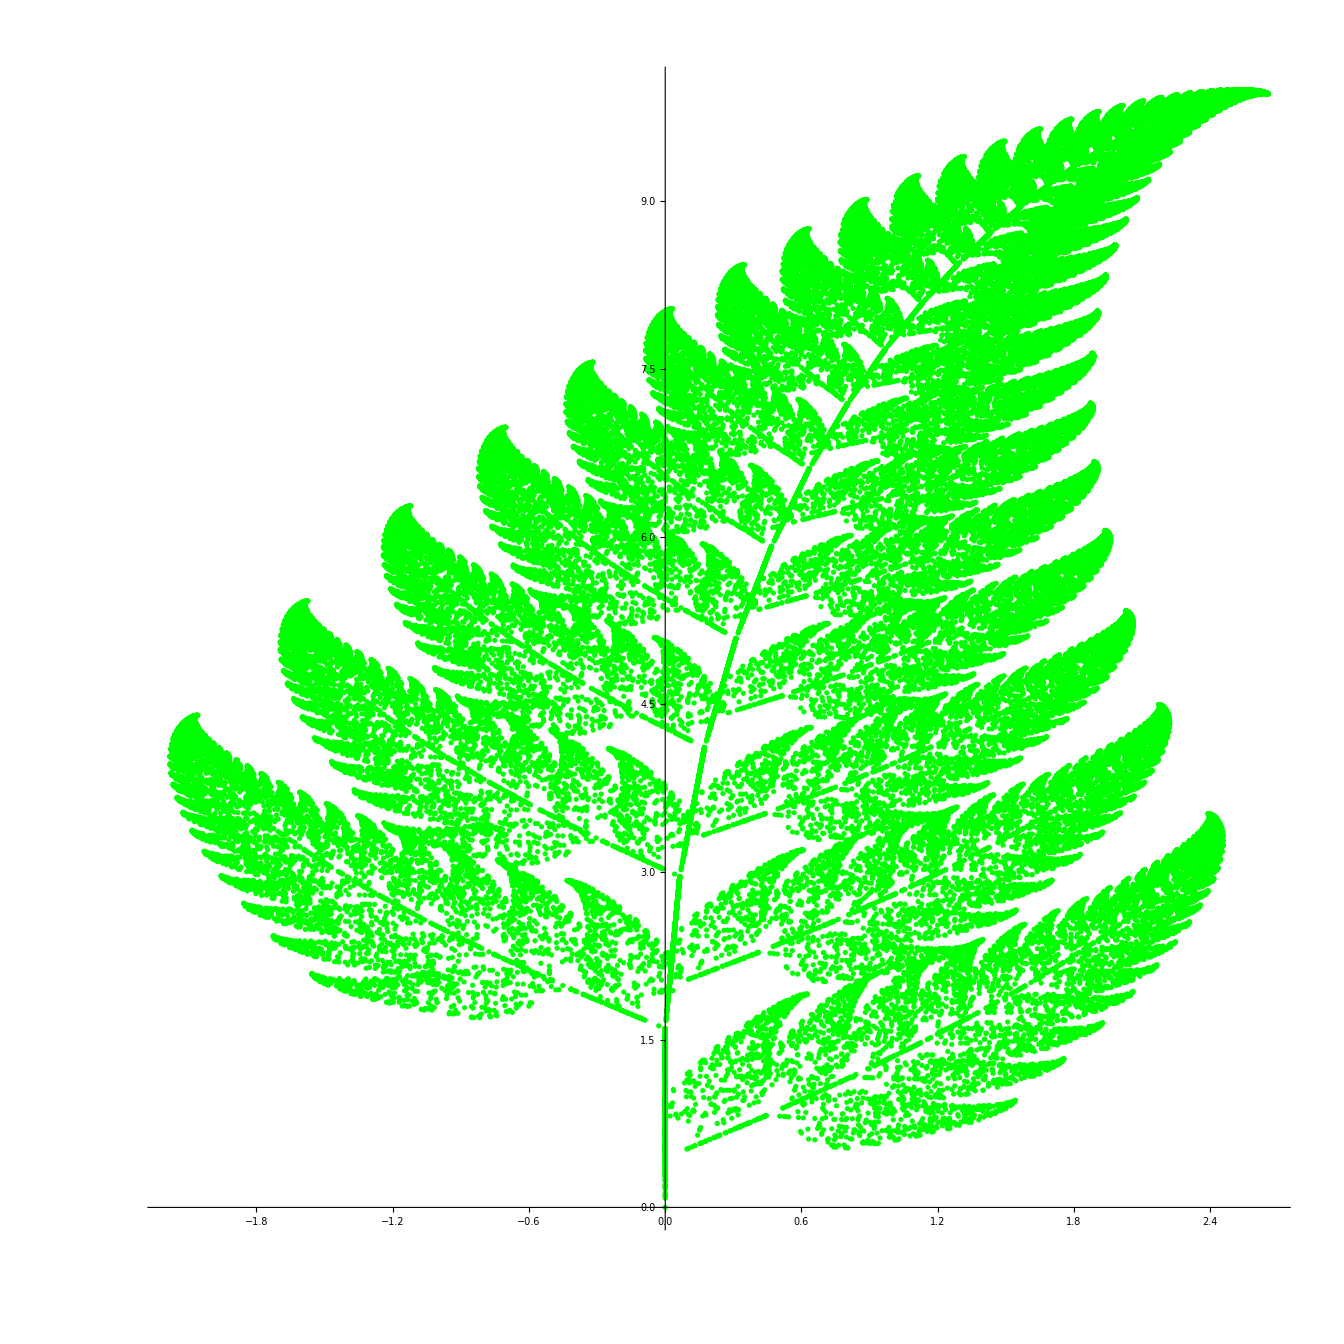

```mathematica
f={({{0.00, 0.00}, {0.00, 0.16}}),({{0.85, 0.04}, {-0.04, 0.85}}),({{0.20, -0.26}, {0.23, 0.22}}),({{-0.15, 0.28}, {0.26, 0.24}})};
fp=({{0.00, 0.00}, {0.00, 1.60}, {0.00, 1.60}, {0.00, 0.44}});
pdist={0.01,0.85,0.07,0.07};
dots={{0.0,0.0}};
Do[
tr=RandomChoice[pdist->Range[4]];
p2=f⟦tr⟧.dots⟦-1⟧+fp⟦tr⟧;
AppendTo[dots,p2];
,{i,100000}];
ListPlot[dots,PlotStyle->Green,AspectRatio->1]
```

## Serpinskei’s Triangle

```mathematica
n=6;
α=0.7;
pts=Table[RotationMatrix[i (2π)/n].{0,1},{i,n}];
dots=pts⟦-1⟧;

Do[
goto=pts⟦RandomInteger[{1,n}]⟧;
AppendTo[dots,(1-α)dots⟦-1⟧+α goto]
,{i,10000}]
```

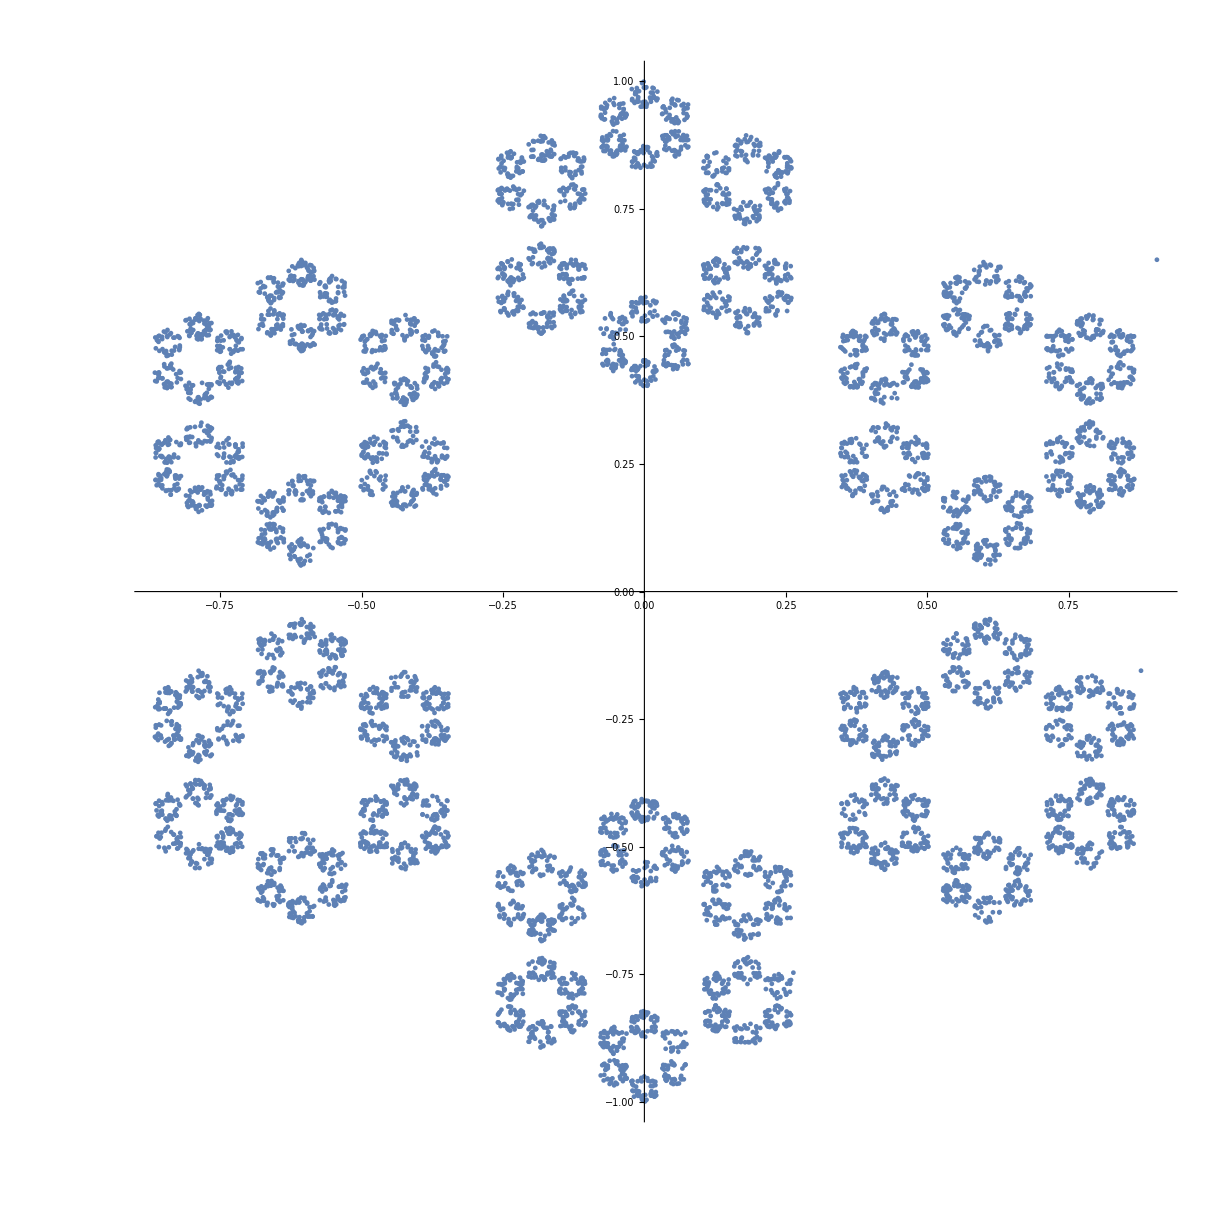

```mathematica
ListPlot[dots,AspectRatio->1]
```